```mathematica
b=0.034;
R=0.045+0.290;
Rin=0.045;
a=5.7;(*slope for Cl*)
B=0.97;(*tip loss*)
A=π*R^2;
Subscript[A, bs]=b*(R-Rin);(*blade aera*)
Subscript[C, D0]=0.015;(*blade profile drag*)
ρ=1.225;
κ=1.15;
MaxRPM=22.2*170;
MaxAoa=15;
MinAoa=4;
THover=13.7;
```

```mathematica
σ[k_,b_,R_]:=(k*b)/(π*R);(*桨叶实度*)
λ[σ_,θ_]:=(σ*a)/16*(√(1+64/(3*σ*a)*θ)-1);(*inflow factor Heli Aero Basic P28, 3.29*)
Subscript[C, T][σ_,θ_]:=(
Subscript[λ, 0]=λ[σ,θ];
0.5*σ*a*(1/3 B^3*θ-1/2 B^2*Subscript[λ, 0]));
(*Blade Mean Lift Coeff; P34; 3.51*)
T[θ_,Ab_,ω_,R_]:=(
Subscript[σ, 0]=σ[k,b,R];
Subscript[C, T][Subscript[σ, 0],θ]*ρ*Ab*(ω*R)^2/Subscript[σ, 0]
);
T[θ_,ω_,k_]:=(
Subscript[σ, 0]=σ[k,b,R];
Subscript[C, T][Subscript[σ, 0],θ]*ρ*Subscript[A, bs]*k*(ω*R)^2/Subscript[σ, 0]
);
AoAwithThrust[T0_,ω_,R0_,Ab_]:=1/(Ab R0^4 ω^4)0.0003470995251616215 (2712.508349385714 R0^2 T0 ω^2+1. Ab R0^3 ω^4+1.9245735344386955*√Ab √(4.882146484665176*^4 R0^5 T0 ω^6+2.699796197367072*^-1 Ab R0^6 ω^8));
OmegabyAoa[T0_,θ0_,R0_,Ab_]:=(1. √T0)/(√(0.011920086196474063 Ab R0+1.0621232037500001 Ab R0^2 θ0-0.011920086196474063 Ab R0 √(1.+183.71886863098203 R0 θ0)));

P[T_,Vt_,Vc_,Ab_,A_]:=((*Thrust,Tip speed, V climb, Total blade Aera, Total Aera, Num of blade*)
Vs=0.5*Vc+√((0.5*Vc)^2+T/(2*ρ*A));
κ*Vs*T+0.125*Subscript[C, D0]*ρ*Ab*Vt^3
);(*Heli aero basic P97*)

Subscript[P, hover][T_,ω_,Ab_,R_]:=(
(*Need to give a omega here;
Note that there is a big range omega and theta;
We need to specify aoa within 5-10 deg to avoid stall
*)
Vt0=R*ω;
P[T,Vt0,0,Ab,π*R^2]
);

(*P hover with fixed Thrust and variable omega*)
omega[rpm_]:=rpm/60*6.28;
```

```mathematica
Aoa[σ_,θ_]:=(θ-λ[σ,θ]/0.75);(*Real aoa on 0.75, use for analyze max load*)
```

桨叶实度:0.0646122

桨盘面积:0.352565

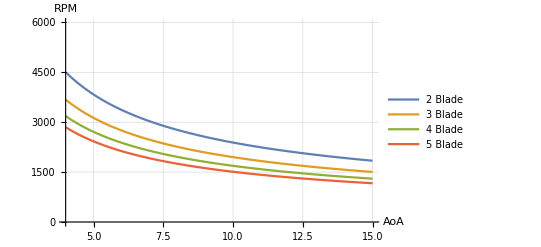

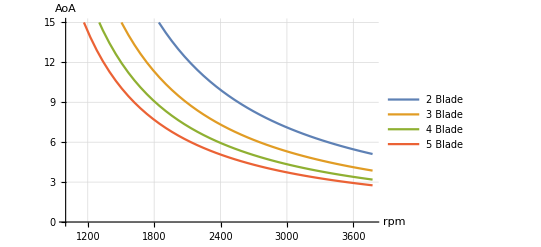

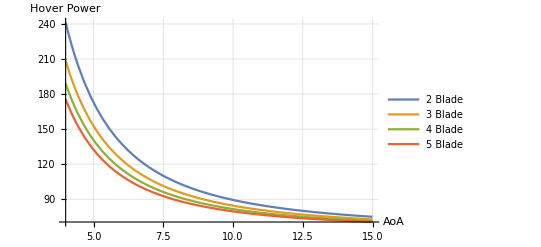

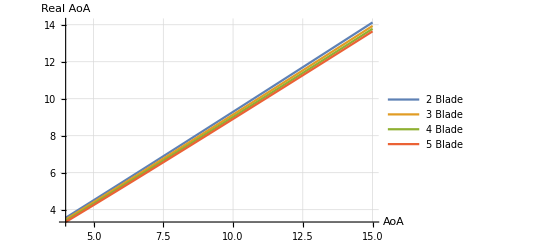

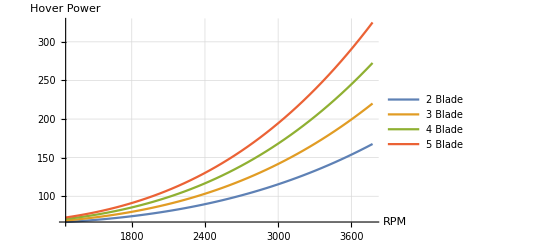

```mathematica
σ0=σ[k,b,R];
S=π*R^2;

Print["桨叶实度:",σ0];
Print["桨盘面积:",S];

bladelegends={"2 Blade", "3 Blade", "4 Blade", "5 Blade"};

express=Table[OmegabyAoa[THover,θ/57.3,R,Subscript[A, bs]*k]/6.28*60,{k,2,5}];
Plot[express,{θ,MinAoa,MaxAoa},PlotLegends->bladelegends,
AxesLabel->{"AoA","RPM"},PlotRange->{Automatic,{0,6000}},GridLines->Automatic]
(*RPM and AoA*)
express=Table[57.3*AoAwithThrust[THover,omega[rpm],R,Subscript[A, bs]*k],{k,2,5}];
p2=Plot[express,{rpm,1000,MaxRPM},PlotLegends->bladelegends,AxesLabel->{"rpm","AoA"},PlotRange->{Automatic,{0,MaxAoa}},GridLines->Automatic]

(*AoA and RPM*)
(*express=Table[T[θ/57.3,omega[rpm],k],{k,2,5}];
Plot3D[express,{θ,0,11},{rpm,0,MaxRPM},PlotLegends->bladelegends,AxesLabel->Automatic,PlotRange->Full]*)

(*AoA and Power*)
express=Table[Subscript[P, hover][THover,OmegabyAoa[THover,θ/57.3,R,Subscript[A, bs]*k],Subscript[A, bs]*k,R],{k,2,5}];
p1=Plot[express,{θ,4,MaxAoa},PlotLegends->bladelegends,
AxesLabel->{"AoA","Hover Power"},GridLines->Automatic]
(*AoA and real AoA*)
express=Table[Aoa[σ[k,b,R],θ],{k,2,5}];
p1=Plot[express,{θ,MinAoa,MaxAoa},PlotLegends->bladelegends,
AxesLabel->{"AoA","Real AoA"},GridLines->Automatic]

express=Table[Subscript[P, hover][THover,omega[rpm],Subscript[A, bs]*k,R],{k,2,5}];
p1=Plot[express,{rpm,MaxRPM/3,MaxRPM},PlotLegends->bladelegends,
AxesLabel->{"RPM","Hover Power"},GridLines->Automatic]
```